# Asymmetric Payoffs Approximations

## Setup:

Clear kernel of unwanted junk!

```mathematica
(*Quit[]*)
```

Setup dynamical expressions. First, I start by determining the average payoff of each host and symbiont phenotype in each environment:

```mathematica
wh1e1 = HM11*s1+Hh11*(1-s1); (*Host 1 environment 1 average payoff is the weighted average of the matching host payoff, and the payoff host 1 receives when interacting with symbiont 2 in environment 1. This means that the host receives a mismatched ρ (symbiont-environment match term) and r (host-symbiont match term)*)
wh2e1 =  Hs21*s1+Hg21*(1-s1);
wh1e2=Hg12*s2+ Hs12*(1-s2);
wh2e2=Hh22*s2+HM22*(1-s2);
```

```mathematica
ws1e1=SM11*h1+Ss11*(1-h1);
ws2e1=Sh21*h1+ Sg21*(1-h1);
ws1e2= Sg12*h2+Sh12*(1-h2);
ws2e2=Ss22*h2+SM22*(1-h2);
```

Modified replicator equation to give the frequency of each strategist in each patch and allow dispersal between the patches:

```mathematica
H1E1d=h1*(1-h1)*(wh1e1-wh2e1)+d*h2-d*h1;
H1E2d= h2*(1-h2)*(wh1e2-wh2e2)-d*h2+d*h1;
S1E1d=s1*(1-s1)*(ws1e1-ws2e1)+d*s2-d*s1;
S1E2d=s2*(1-s2)*(ws1e2-ws2e2)-d*s2+d*s1;
```

### Asymmetric Simulation

```mathematica
dynsysasym[h10_,h20_,s10_,s20_,HM11_,HM22_,Hg12_,Hg21_,Hh11_,Hh22_,Hs12_,Hs21_, SM11_,SM22_, Ss11_,Ss22_,Sh21_,Sh12_,Sg21_,Sg12_,d_]:= {h1'[t]==-d h1[t]+d h2[t]+(-1+h1[t]) h1[t] (Hg21+Hh11 (-1+s1[t])-Hg21 s1[t]+(-HM11+Hs21) s1[t]),h2'[t]==d h1[t]-d h2[t]+(-1+h2[t]) h2[t] (HM22+Hs12 (-1+s2[t])+(-Hg12+Hh22) s2[t]-HM22 s2[t]),s1'[t]==-d s1[t]+d s2[t]-(-1+s1[t]) s1[t] ((-1+h1[t]) Sg21+Ss11-h1[t] (Sh21-SM11+Ss11)),s2'[t]==d s1[t]-d s2[t]-(-1+s2[t]) s2[t] (Sh12-SM22+h2[t] (Sg12-Sh12+SM22-Ss22)),h1[0]==h10,h2[0]==h20,s1[0]==s10,s2[0]==s20}

PlotWFNasym[h10_,h20_,s10_,s20_,HM11_,HM22_,Hg12_,Hg21_,Hh11_,Hh22_,Hs12_,Hs21_, SM11_,SM22_, Ss11_,Ss22_,Sh21_,Sh12_,Sg21_,Sg12_,dmax,deltad]:={tmax=10000;
dynsol=ParametricNDSolveValue[dynsysasym[h10,h20,s10,s20,HM11,HM22,Hg12,Hg21,Hh11,Hh22,Hs12,Hs21, SM11,SM22, Ss11,Ss22,Sh21,Sh12,Sg21,Sg12,d],{h1[tmax],h2[tmax],s1[tmax],s2[tmax]},{t,0,tmax},{d,h10},AccuracyGoal->4,PrecisionGoal->4];
fxntable2=Table[{d,h10,dynsol[d,h10]},{h10,0,1,0.01},{d,0,dmax,deltad}]~Flatten~1;
ds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
s1e1v=fxntable2[[All,3,3]];
s1e2v=fxntable2[[All,3,4]];
h1e1p=Transpose@{ds,averagef,h1e1v};
h1e2p=Transpose@{ds,averagef,h1e2v};
s1e1p=Transpose@{ds,averagef,s1e1v};
s1e2p=Transpose@{ds,averagef,s1e2v};
stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h2",h1e2p},{"s2",s1e2p}};
plotlist={};
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-deltad,dmax+deltad},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];
Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial Frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final Frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]}
```

### Symmetric Simulation

```mathematica
dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]:= {h1e1'[t]==-d h1e1[t]+d h1e2[t]+(1-h1e1[t]) h1e1[t] (-Hg (1-s1e1[t])+Hh (1-s1e1[t])+HM s1e1[t]-Hs s1e1[t]),h1e2'[t]==d h1e1[t]-d h1e2[t]+(1-h1e2[t]) h1e2[t] (-HM (1-s1e2[t])+Hs (1-s1e2[t])+Hg s1e2[t]-Hh s1e2[t]),s1e1'[t]==-d s1e1[t]+(Ss (1-h1e1[t])+Sg (-1+h1e1[t])-Sh h1e1[t]+SM h1e1[t]) (1-s1e1[t]) s1e1[t]+d s1e2[t],s1e2'[t]==d s1e1[t]-d s1e2[t]+(Sh (1-h1e2[t])-SM (1-h1e2[t])+Sg h1e2[t]-Ss h1e2[t]) (1-s1e2[t]) s1e2[t],h1e1[0]==h1e10,h1e2[0]==h1e20,s1e1[0]==s1e10,s1e2[0]==s1e20}
```

```mathematica
PlotWFN[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_,dmax_,deltad_]:={
tmax=10000;
(*dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e20,s1e10,s1e20,HM,Hg,Hh,Hs, SM, Sg,Sh,Ss],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10},AccuracyGoal->5,PrecisionGoal->3];
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.01},{d,0,dmax,deltad}]~Flatten~1;
ds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
s1e1v=fxntable2[[All,3,3]];
s1e2v=fxntable2[[All,3,4]];
h1e1p=Transpose@{ds,averagef,h1e1v};
h1e2p=Transpose@{ds,averagef,h1e2v};
s1e1p=Transpose@{ds,averagef,s1e1v};
s1e2p=Transpose@{ds,averagef,s1e2v};
stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h2",h1e2p},{"s2",s1e2p}};
plotlist={};
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-deltad,dmax+deltad},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];
Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial Frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final Frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]
}
```

## Simulations:

### Payoffs taken exactly from Johnson et al. 2010.

```mathematica
(*symb payoffs*)
SM11 = 87.5;
SM22 = 87.2;
Ss11 = 82.89999999999999;
Ss22 = 82.83333333333333;
Sg12 = 68.75;
Sg21 = 47.81666666666666;
Sh12 = 64.23333333333333;
Sh21 = 46.5;
(*Within environment deltas: *)
DeltaSmh1= 41.0;(*Sm11-Ss21*)
DeltaSmh2 = 22.96666666666667;(*Sm22-Ss12*)
DeltaSgs1=-14.083333333333329;(*Sg12-Ss21*)
DeltaSgs2=-35.08333333333333(*Sg21-Ss12*);
sum=DeltaSmh1+DeltaSmh2+DeltaSgs1+DeltaSgs2(*Sum of all delta terms between each environment*)
```

14.8

```mathematica
(*Host payoffs*)
HM11 = 4.833333333333333;
HM22 = 2.518;
Hh11 = 3.5433333333333334;
Hh22 = 3.3683333333333336;
Hg12 = 3.1750000000000003;
Hg21 = 3.158333333333333;
Hs12 = 2.308333333333333;
Hs21 = 4.555;
```

### Simulations using the model with symmetric payoff differences:

Behavior of symmetric model with averages of payoffs:

```mathematica
(*Because in our data analysis we found that ΔHms=0 and ΔHgh=0 in both environments, it means that there are no significant differences between any of the Hm and Hs terms, and the Hg and Hh terms. Therefore, I just use the average of these terms for the host parameters when necessary. In this symmetric simulation, I'm using the average of the symbiont payoff terms across each symbiont genotype.  *)
dmax=25;
deltad=1;
(*[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)

(*Payoff Fitness values here are the average of each 'host' plant and 'symbiont' fungus genotype*)
PlotWFN[h1e10,h1e10,h1e10,h1e10,(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4,(SM11+SM22)/2,(Sg12+Sg21)/2,(Sh12+Sh21)/2,(Ss11+Ss22)/2,dmax,deltad]
(*Export["dummy.png",%];
b=Import["dummy.png"];
fontsize=60;
text={Graphics[Text[Style["a)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["b)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["c)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["d)",Directive[FontSize->32],FontFamily->"Times",FontColor-> Black]]]};
panels={Scaled[{0.1,0.94}],Scaled[{0.5,0.94}],Scaled[{0.1,0.53}],Scaled[{0.5,0.53}]};
c=ImageCompose[b,text,panels]*)
(*Export["sym.png",c]*)
```

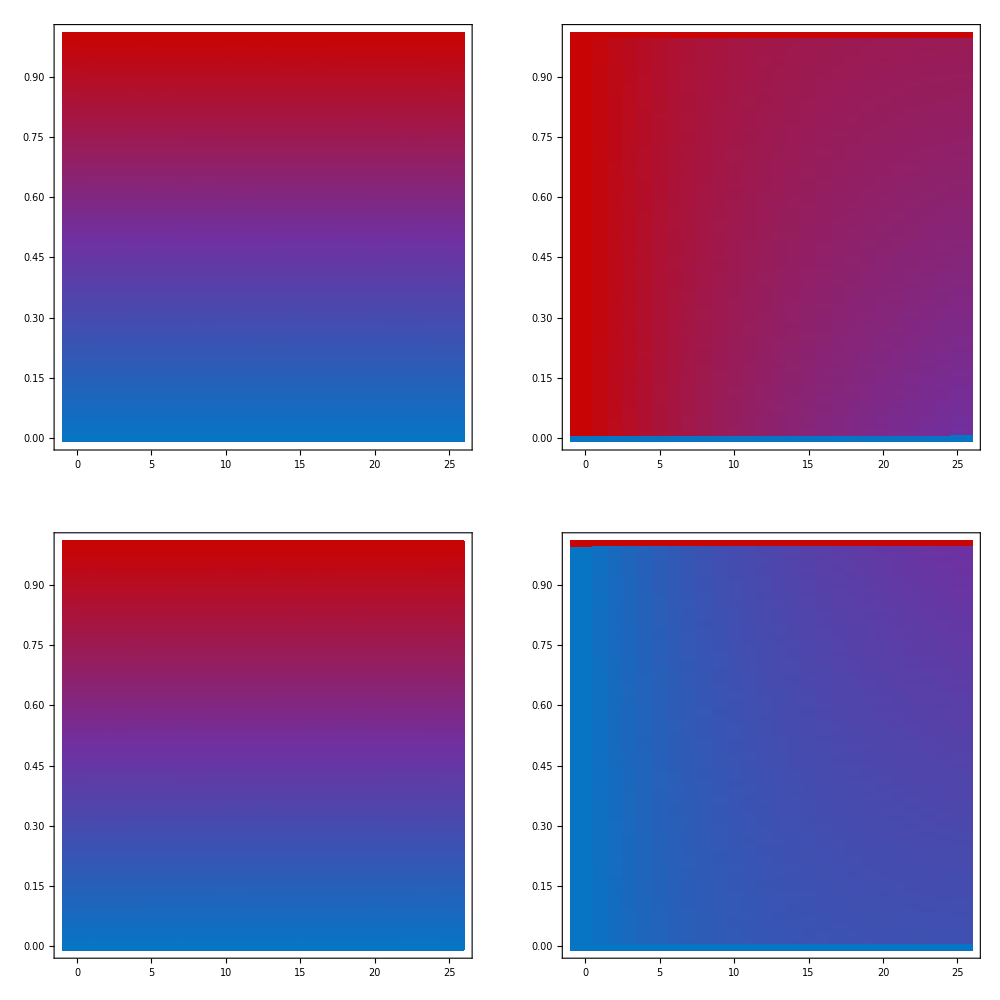
```mathematica
{PlotWFN[h1e10,h1e10,h1e10,h1e10,(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4,(SM11+SM22)/2,(Sg12+Sg21)/2,(Sh12+Sh21)/2,(Ss11+Ss22)/2,dmax,deltad]-Graphics-"Initial Frequency""Dispersal"""}
```

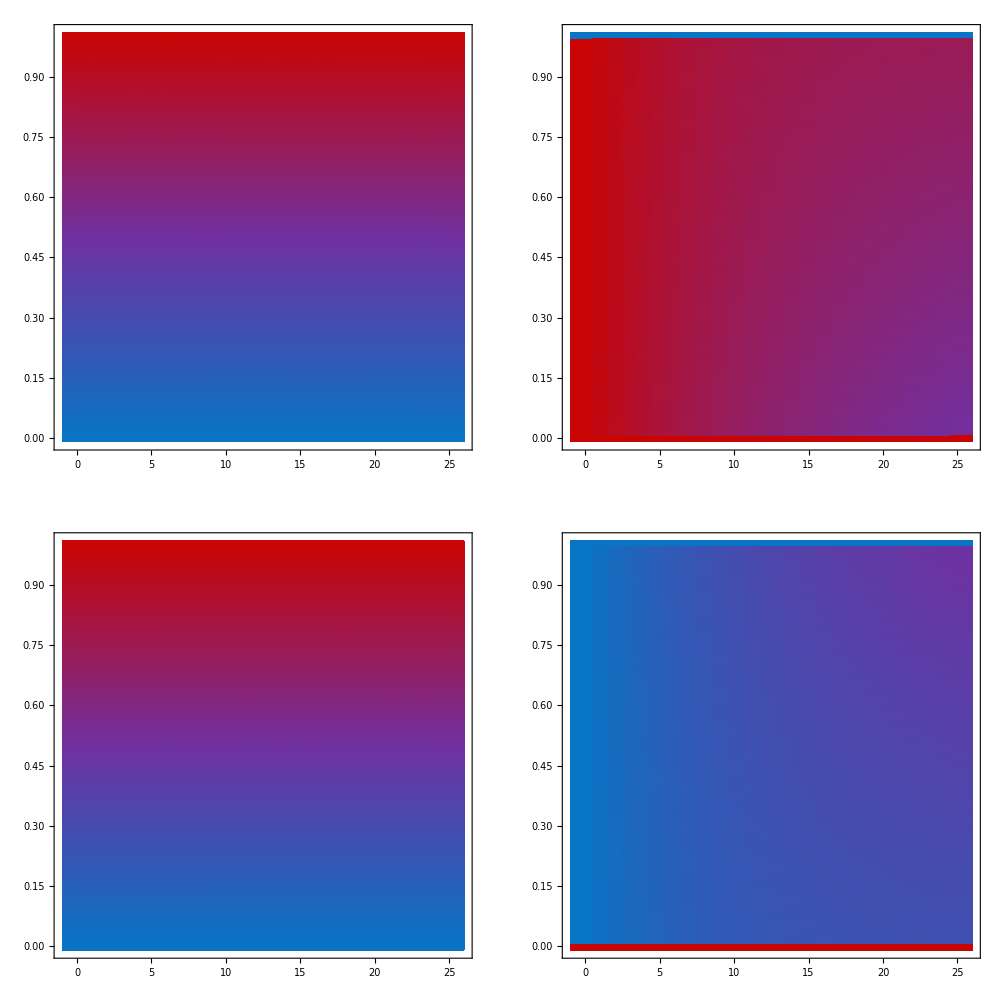
{-Graphics-Initial FrequencyDispersal}

```mathematica
PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4,(SM11+SM22)/2,(Sg12+Sg21)/2,(Sh12+Sh21)/2,(Ss11+Ss22)/2,dmax,deltad]
```

### Simulations using the model with asymmetric payoff differences:

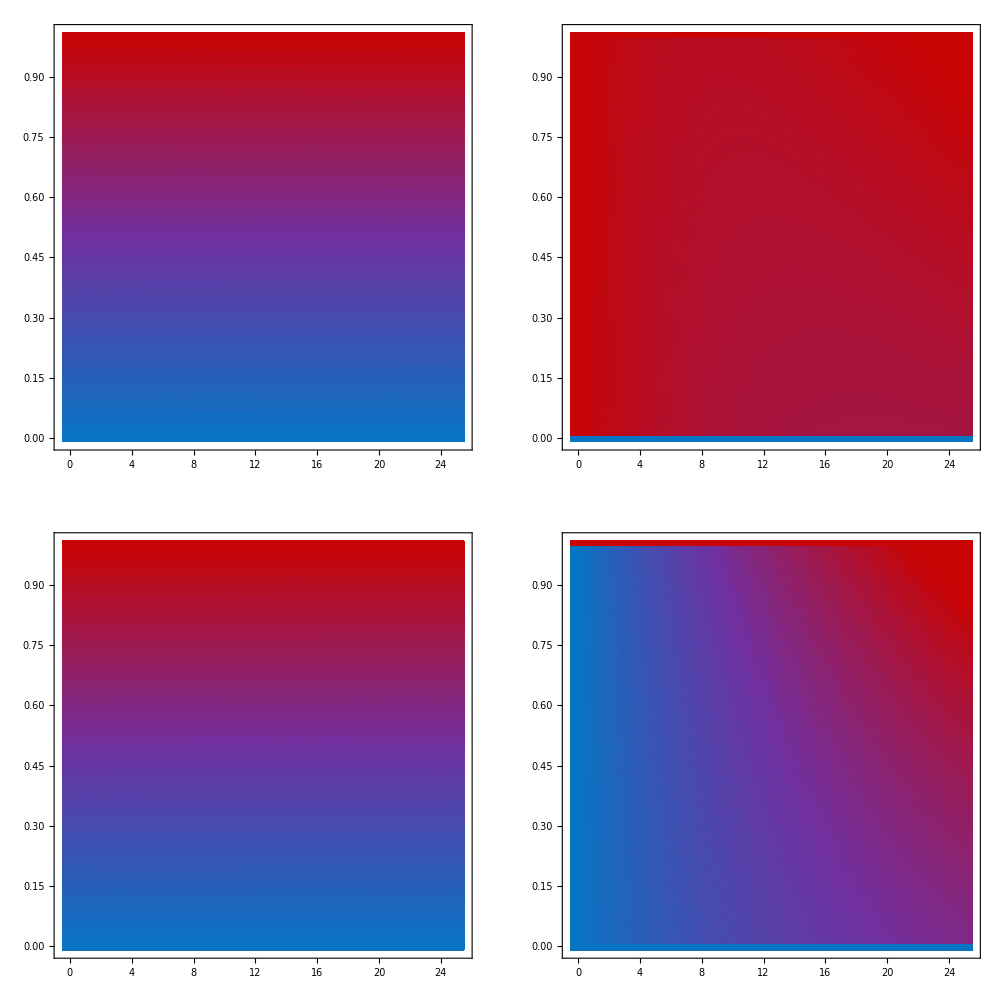
{-Graphics-Initial FrequencyDispersal}

```mathematica
dmax=25;
deltad=0.5;
PlotWFNasym[h10,h10,h10,h10,(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4,(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4, SM11,SM22, Ss11,Ss22,Sh21,Sh12,Sg21,Sg12,dmax,deltad]
(*Export["dummy.png",%];
b=Import["dummy.png"];
fontsize=60;
text={Graphics[Text[Style["a)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["b)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["c)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["d)",Directive[FontSize->32],FontFamily->"Times",FontColor-> Black]]]};
panels={Scaled[{0.1,0.94}],Scaled[{0.5,0.94}],Scaled[{0.1,0.53}],Scaled[{0.5,0.53}]};
c=ImageCompose[b,text,panels]
Export["asym.png",c]*)
```

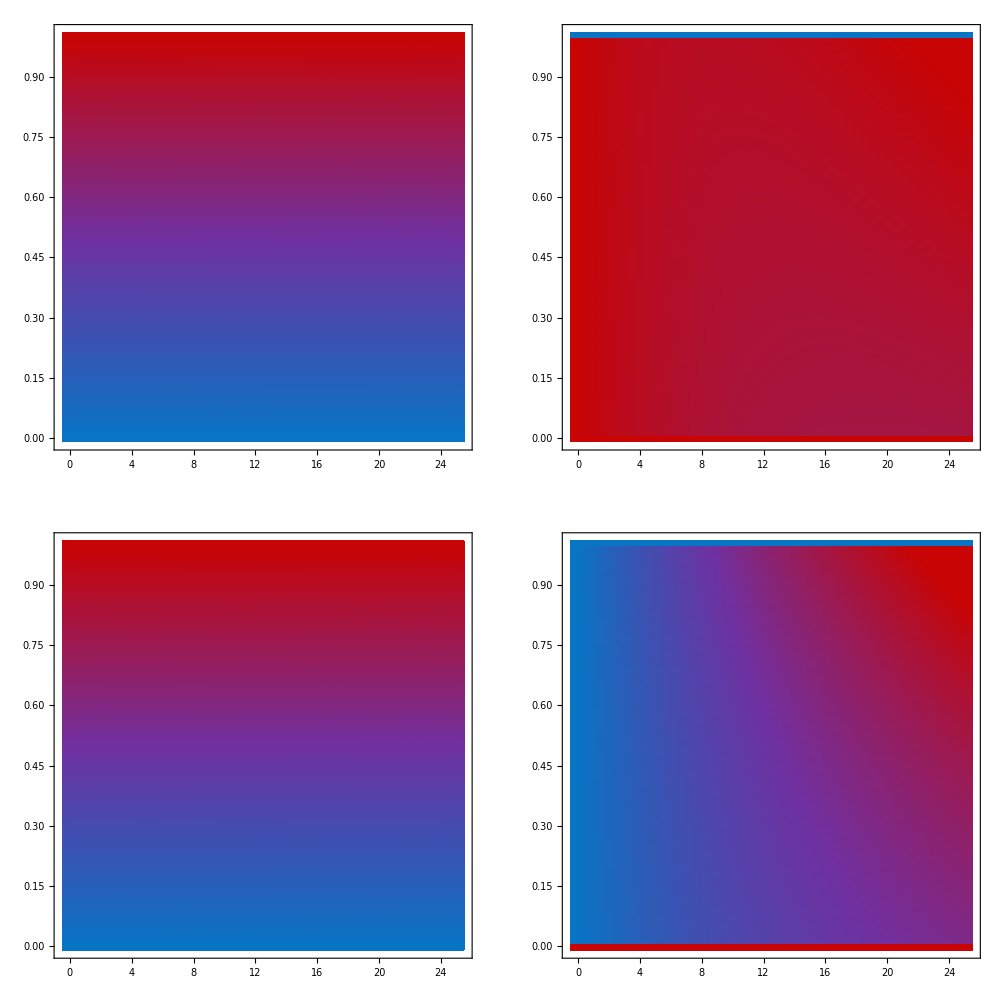
{-Graphics-Initial FrequencyDispersal}

```mathematica
dmax=25;
deltad=0.5;
PlotWFNasym[h10,h10,(1-h10),(1-h10),(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4,(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4, SM11,SM22, Ss11,Ss22,Sh21,Sh12,Sg21,Sg12,dmax,deltad]
```

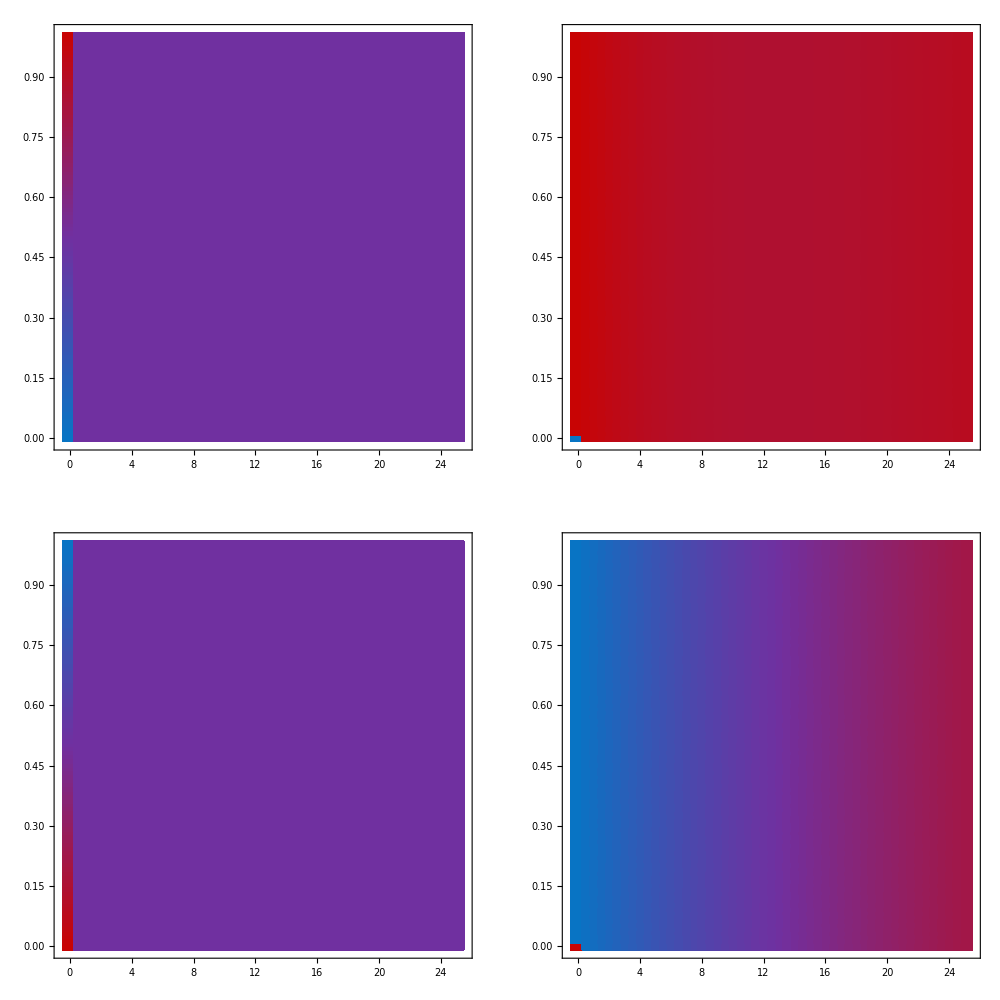
{-Graphics-Initial FrequencyDispersal}

```mathematica
dmax=25;
deltad=0.5;
PlotWFNasym[h10,(1-h10),h10,(1-h10),(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4,(HM11+HM22+Hs12+Hs21)/4,(Hg12+Hg21+Hh11+Hh22)/4,(Hg12+Hg21+Hh11+Hh22)/4,(HM11+HM22+Hs12+Hs21)/4, SM11,SM22, Ss11,Ss22,Sh21,Sh12,Sg21,Sg12,dmax,deltad]
```